```mathematica
GeneralLinearAnizatropy[α0_,U0_,χ0_,θ0_,β0_,P0_]:= 
Module[{α=α0,U=U0,χ=χ0,θ=θ0,β=β0,P=P0},
(*α - dissipation, α=ν/ω, ω->ω(1+ⅈα)*)
(*U - anizatropy: p^2=4πe^2*n/m, b=eB/(mc), v=p^2/ω^2, u=b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα)*)
(*χ - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L=1*) 
(*θ - ngel between wave vector and XOZ*)
(*β - angle between wave vector and magnetic field direction*)
(*P - wave polarisation; 2d-vector*)

(*=====================================================================================================================*)

(*Plasma configuration*)
X=3;(*plasma boundary*)
Δ=0.05;(*smoothing width, in parts of plasma whight*)
n=1/Δ; smoothingFunc=Function[x,(1-(x/X)^(2n))^-1]; v=Function[x,((X^2-x^2)/(X^2-1))*smoothingFunc[x]*(1-ⅈ*α)]; u=U(1-ⅈ*α);
Eps=({{1-v[x]/(1-u), ⅈ(√u)/(1-u)v[x], 0}, {-ⅈ(√u)/(1-u)v[x], 1-v[x]/(1-u), 0}, {0, 0, 1-v[x]}}); (*({{1-v[x]/(1-u), ⅈ(√u)/(1-u)v[x], 0}, {-ⅈ(√u)/(1-u)v[x], 1-v[x]/(1-u), 0}, {0, 0, 1-v[x]}})*)

(*=====================================================================================================================*)

(*Wave configuration*)
A=1;(*wave magnitude*)
k=χ({{Cos[θ]Sin[β]}, {Sin[θ]}, {Cos[θ]Cos[β]}})ᵀ[[1]];(*wave vector*)
Ε=A/Norm[P]({{Cos[β], -Sin[θ]Sin[β]}, {0, Cos[θ]}, {-Sin[β], -Sin[θ]Cos[β]}}).P; (*Electric field (!!!ESCAPE_SEQUENCE!!!)*)
Β=(k×Ε)/χ;(*Magnetic field (!!!ESCAPE_SEQUENCE!!!)*)

(*=====================================================================================================================*)

(*Maxwell equations*)
GeneralSystem = {
(*Ex[x]*Eps[x][[1,1]]+Ey[x]*Eps[x][[1,2]]==kz*By[x]-ky*Bz[x], Bx[x]==ky*Ez[x]-kz*Ey[x],*)
Ey'[x]==ⅈ*χ*(ky*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]+Bz[x]),(*Ey'[x]==ⅈ*χ*(ky*Ex[x]+Bz[x])*)
Ez'[x]==ⅈ*χ*(kz*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]-By[x]),(*Ez'[x]==ⅈ*χ*(kz*Ex[x]-By[x])*)
By'[x]==ⅈ*χ*(ky*(ky*Ez[x]-kz*Ey[x])-Eps[[3,3]]*Ez[x]),(*By'[x]==ⅈ*χ*(ky*Bx[x]-Eps[x][[3,3]]*Ez[x])*)
Bz'[x]==ⅈ*χ*(kz*(ky*Ez[x]-kz*Ey[x])+Eps[[2,1]]*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]+Eps[[2,2]]*Ey[x])(*Bz'[x]==ⅈ*χ*(kz*Bx[x]+Eps[x][[2,1]]*Ex[x]+Eps[x][[2,2]]*Ey[x])*)
}/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ};

GeneralInitials = {Ey[2X]==Ε[[2]],Ez[2X]==Ε[[3]],By[2X]==Β[[2]],Bz[2X]==Β[[3]]};
Sol=NDSolveValue[{GeneralSystem,GeneralInitials},{Ey,Ez,By,Bz},{x,-2X,2X}];

(*=====================================================================================================================*)

(*Polarisation rotations*)
$Transmitted=If[P[[1]]==0,Conjugate[P[[2]]]/Abs[P[[2]]],Conjugate[P[[1]]]/Abs[P[[1]]]]({{P[[1]]/Norm[P]}, {P[[2]]/Norm[P]}})ᵀ[[1]];(*Transmitted wave*)
$IW=(({{Cos[β], 0, -Sin[β]}, {-Sin[β]Sin[θ], Cos[θ], -Cos[β]Sin[θ]}}).({{(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]}, {Ey[x]}, {Ez[x]}}))ᵀ[[1]]/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ,Ey[x]->Sol[[1]][x],Ez[x]->Sol[[2]][x],By[x]->Sol[[3]][x],Bz[x]->Sol[[4]][x]};
$IP=({{a/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==$IW[[1]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[$IW[[1]],x]/.x->(-2X)},{a,b}][[1]]}, {a/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==$IW[[2]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[$IW[[2]],x]/.x->(-2X)},{a,b}][[1]]}})ᵀ[[1]];
$Initial=If[$IP[[1]]==0,Conjugate[$IP[[2]]]/Abs[$IP[[2]]],Conjugate[$IP[[1]]]/Abs[$IP[[1]]]]({{($IP[[1]])/Norm[$IP]}, {($IP[[2]])/Norm[$IP]}})ᵀ[[1]];(*Initial wave*)
$RW=(({{Cos[π-β], 0, -Sin[π-β]}, {-Sin[π-β]Sin[-θ], Cos[-θ], -Cos[π-β]Sin[-θ]}}).({{(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]}, {Ey[x]}, {Ez[x]}}))ᵀ[[1]]/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ,Ey[x]->Sol[[1]][x],Ez[x]->Sol[[2]][x],By[x]->Sol[[3]][x],Bz[x]->Sol[[4]][x]};
$RP=({{b/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==$RW[[1]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[$RW[[1]],x]/.x->(-2X)},{a,b}][[1]]}, {b/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==$RW[[2]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[$RW[[2]],x]/.x->(-2X)},{a,b}][[1]]}})ᵀ[[1]];
$Reflected=If[$RP[[1]]==0,Conjugate[$RP[[2]]]/Abs[$RP[[2]]],Conjugate[$RP[[1]]]/Abs[$RP[[1]]]]({{($RP[[1]])/Norm[$RP]}, {($RP[[2]])/Norm[$RP]}})ᵀ[[1]];(*Reflected wave*)
(*Dissipation*)
$Dissipation=1-Norm[{$RP[[1]],$RP[[2]],0}×({0,0,1}×{$RP[[1]],$RP[[2]],0})]/Norm[{$IP[[1]],$IP[[2]],0}×({0,0,1}×{$IP[[1]],$IP[[2]],0})];

(*=====================================================================================================================*)

{Eps,k,Sol,$Initial,$Reflected,$Transmitted,$Dissipation}
]
```

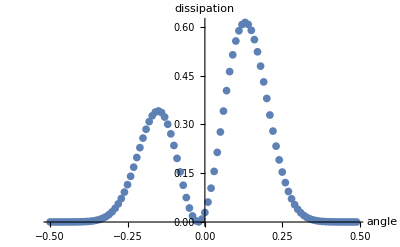

```mathematica
Dissipation={};
Θbegining=-0.5;Θend=0.5;Θnstep=100;
ProgressIndicator[Dynamic[(θ-Θbegining)/(Θend-Θbegining)]]
For[θ=Θbegining,θ<Θend,θ+=(Θend-Θbegining)/Θnstep,
Dissipation=Append[Dissipation,{θ,GeneralLinearAnizatropy[0.000001,0.00001,30,θ,π/2,{0,1}][[7]]}];
];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation}]
(*ListPlot[Table[{EtalonDissipation[[i]][[1]],Abs[(EtalonDissipation[[i]][[2]]-Dissipation[[i]][[2]])/(EtalonDissipation[[i]][[2]])]},{i,100}],PlotRange->Full]*)
```

```mathematica
Dissipation={};
Ibegining=-20;Iend=20;Instep=100;
Θbegining=-0.4;Θend=0.4;Θnstep=100;
ProgressIndicator[Dynamic[(i-Ibegining)/(Iend-Ibegining)]]
υ=Function[x,If[x≤0,Exp[x]/2,1-Exp[-x]/2]];
For[i=Ibegining,i<Iend,i+=(Iend-Ibegining)/Instep,
For[θ=Θbegining,θ<Θend,θ+=(Θend-Θbegining)/Θnstep,
Dissipation=Append[Dissipation,{θ,i,GeneralLinearAnizatropy[0.000001,υ[i],30,θ,π/2,{0,1}][[7]]}];
];
];
ListPlot3D[Dissipation,PlotRange->Full,AxesLabel->{angle,anizatropy,dissipation}]
```

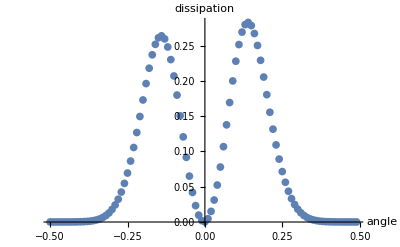

```mathematica
Dissipation={};
begining=-0.5;end=0.5;nstep=100;
ProgressIndicator[Dynamic[(θ-begining)/(end-begining)]]
For[θ=begining,θ<end,θ+=(end-begining)/nstep,
solForB=GeneralLinearAnizatropy[0.000001,0.0000001,30,θ,π/2,{0,1}][[3]][[4]];
fourier=NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==solForB[-2X],ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==solForB'[-2X]},{a,b}];
Dissipation=Append[Dissipation,{θ,(1-Abs[b/.fourier]/Abs[a/.fourier])[[1]]}];
];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation}]
```

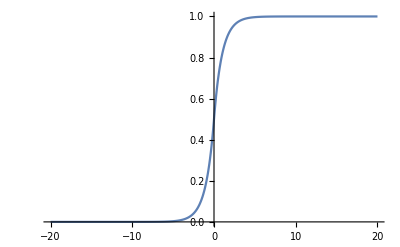

```mathematica
Plot[If[x≤0,Exp[x]/2,1-Exp[-x]/2],{x,-20,20},PlotRange->Full]
```

```mathematica
Table[N[If[x≤0,Exp[x]/2,1-Exp[-x]/2],20]/.x->(-20+i),{i,0,40,0.4}]
```

{1.03058×10^-9,1.53744×10^-9,2.29359×10^-9,3.42164×10^-9,5.10448×10^-9,7.61499×10^-9,1.13602×10^-8,1.69475×10^-8,2.52827×10^-8,3.77173×10^-8,5.62676×10^-8,8.39414×10^-8,1.25226×10^-7,1.86815×10^-7,2.78695×10^-7,4.15764×10^-7,6.20248×10^-7,9.25301×10^-7,1.38039×10^-6,2.05929×10^-6,3.07211×10^-6,4.58304×10^-6,6.8371×10^-6,0.0000101998,0.0000152162,0.0000227,0.0000338644,0.0000505197,0.0000753665,0.000112434,0.000167731,0.000250226,0.000373293,0.000556888,0.000830779,0.00123938,0.00184893,0.00275828,0.00411487,0.00613867,0.00915782,0.0136619,0.0203811,0.030405,0.045359,0.0676676,0.100948,0.150597,0.224664,0.33516,0.5,0.66484,0.775336,0.849403,0.899052,0.932332,0.954641,0.969595,0.979619,0.986338,0.990842,0.993861,0.995885,0.997242,0.998151,0.998761,0.999169,0.999443,0.999627,0.99975,0.999832,0.999888,0.999925,0.999949,0.999966,0.999977,0.999985,0.99999,0.999993,0.999995,0.999997,0.999998,0.999999,0.999999,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
10*100/60 //N
```

16.6667

```mathematica
Clear[x]
```